### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/21

### Keywords

Details

# Model 2.1-2.2

Model 2.1-2.2 are the model for the dynamics of malaria parasites in a patient during treatment with mefloquine. It was proposed by Simpson J. A., et al.(2000 Mefloquine pharmacokinetic-pharmacodynamic models: implications for dosing and resistance Antimicrobial agents and chemotherapy 44, 3414-3424 ).

## Model 2.1

The output of model 2.1 is  the number of parasites overtime which calculated from this equation

-Graphics-

model | model ID
p0 | the initial load of parasites
a | a growth rate constant
k | the terminal elimination rate of the drug
k1 | the maximum parasite killing rate (results from mefloquine)
c0 | the initial concentration of mefloquine
gamma | a constant (see above equation)
c50 | the concentration which kill 50% of the parasites
outform | the output form (model 2.1 has one output form (0))

The list of parameters of model 2.1.

Example of the output of model 2.1

******INDIVARIA*****

model: 2.1

outform: 0

********************

model: 2.1

p0: 12.

a: 1.15

k: 0.036

k1: 3.45

c0: 1200

gamma: 2.5

c50: 665.4

outform: 0

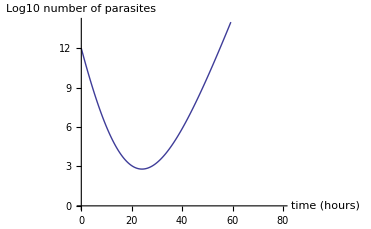

```mathematica
lsout=IDVL["mod2_1.in"];
ListPlot[lsout,Joined->True,PlotRange->{0,14},AxesLabel->{"time (hours)","Log10 number of parasites"}]
```

## Model 2.2

Model 2.2 is the modified version of model 2.1. The output of model 2.2 is the list of number of parasites over time. It is calculated from the equation below.

-Graphics--Graphics-

model | model ID
p0 | the initial load of parasites
a | a growth rate constant
k | the terminal elimination rate of the drug
k1 | the maximum parasite killing rate (results from mefloquine)
c0 | the initial concentration of mefloquine
gamma | a constant (see above equation)
c50 | the concentration which kill 50% of the parasites
mic | the minimum inhibitary concentration
outform | the output form (model 2 has one output form (0))

The list of parameters of model 2.2.

Example of the output from model 2.2

******INDIVARIA*****

model: 2.2

outform: 0

********************

model: 2.2

p0: 12.

a: 1.15

k: 0.036

k1: 3.45

c0: 1200

gamma: 2.5

c50: 665.4

mic: 504.3

outform: 0

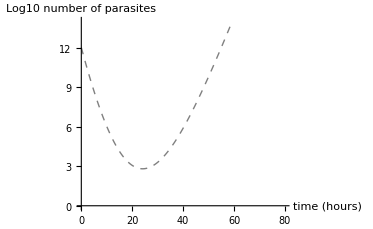

```mathematica
lsout=IDVL["mod2_2.in"];
ListPlot[lsout,Joined->True,PlotRange->{0,14},AxesLabel->{"time (hours)","Log10 number of parasites"},PlotStyle->{Dashed,Gray}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses